```mathematica
(*------ Change to won directory-----*)
SetDirectory["~/Dropbox/Doublesex/Resistance/GeneralMetapop/build"];

allelefreq[tot_]:=Block[{w,dd,r,A,B,tottot},
w=Table[tot[[i,2]]+.5tot[[i,3]]+.5tot[[i,5]]+tot[[i,8]]+.5tot[[i,9]]+.5tot[[i,11]]+tot[[i,14]]+.5tot[[i,15]]+.5tot[[i,17]],{i,Length[tot]}];
dd=Table[tot[[i,4]]+.5tot[[i,3]]+.5tot[[i,7]]+tot[[i,10]]+.5tot[[i,9]]+.5tot[[i,13]]+tot[[i,16]]+.5tot[[i,15]]+.5tot[[i,19]],{i,Length[tot]}];
r=Table[tot[[i,6]]+.5tot[[i,5]]+.5tot[[i,7]]+tot[[i,12]]+.5tot[[i,11]]+.5tot[[i,13]]+tot[[i,18]]+.5tot[[i,17]]+.5tot[[i,19]],{i,Length[tot]}];
A=Table[Total[tot[[i,2;;7]]]+0.5Total[tot[[i,8;;13]]],{i,Length[tot]}];
tottot=(0.1+Total[Transpose[tot[[All,2;;19]]]]);
N[{w/tottot,dd/tottot,r/tottot,A/tottot,(tottot-A)/tottot}]];
(*-----------------------------------*)

(*------ Make parameter file-----*)
xibli={0.,0.2,0.4,0.6};
Do[pa=Flatten[{numruns=10,maxT=15000,NumPat=200,muJ=0.05,muA=0.125,beta=100,theta=9,meanTL=0.0667,mindev=10,gamma=(1-0.95)/2,xiA=0.8,xiB=xibli[[xx]],eA=0.95,eB=0.95,drivertime=100,NumDriver=1000,NumDriverPat=1,d=0.0005,Ld=0.15,psi=0,muAES=0.9,thide1=300,thide2=350,twake1=140,twake2=170,al0=5000,al0var=0.,al1=0,amp=0,resp=1,recstart=10,recend=10000,recIntGlob=10,recIntLoc=730,recsitesfreq=1,set=xx-1,"t","r"}];
Export["Par"<>ToString[set]<>".csv",pa,"CSV","TextDelimiters"->""],{xx,4}];
```

```mathematica
(*------ Make parameter file-----*)
xibli={0.,0.2,0.4,0.6};
Do[pa=Flatten[{numruns=1,maxT=10000,NumPat=200,muJ=0.05,muA=0.125,beta=100,theta=9,meanTL=0.0667,mindev=10,gamma=(1-0.95)/2,xiA=0.8,xiB=xibli[[xx]],eA=0.95,eB=0.95,drivertime=100,NumDriver=1000,NumDriverPat=1,d=0.0005,Ld=0.15,psi=0,muAES=0.9,thide1=300,thide2=350,twake1=140,twake2=170,al0=5000,al0var=0.,al1=0,amp=0,resp=1,recstart=10,recend=10000,recIntGlob=1,recIntLoc=25,recsitesfreq=1,set=100+xx-1,"t","r"}];
Export["Par"<>ToString[set]<>".csv",pa,"CSV","TextDelimiters"->""],{xx,4}];
```

```mathematica
pa=Flatten[{numruns=1,maxT=10000,NumPat=200,muJ=0.05,muA=0.125,beta=100,theta=9,meanTL=0.0667,mindev=10,gamma=(1-0.95)/2,xiA=0,xiB=0,eA=0.95,eB=0.5,drivertime=100,NumDriver=1000,NumDriverPat=1,d=0.0005,Ld=0.15,psi=0,muAES=0.9,thide1=300,thide2=350,twake1=140,twake2=170,al0=5000,al0var=0.,al1=0,amp=0,resp=1,recstart=10,recend=10000,recIntGlob=1,recIntLoc=25,recsitesfreq=1,set=200,"t","r"}];
Export["Par"<>ToString[set]<>".csv",pa,"CSV","TextDelimiters"->""];

pa=Flatten[{numruns=1,maxT=10000,NumPat=200,muJ=0.05,muA=0.125,beta=100,theta=9,meanTL=0.0667,mindev=10,gamma=(1-0.95)/2,xiA=0,xiB=0,eA=0.95,eB=0,drivertime=100,NumDriver=1000,NumDriverPat=1,d=0.0005,Ld=0.15,psi=0,muAES=0.9,thide1=300,thide2=350,twake1=140,twake2=170,al0=5000,al0var=0.,al1=0,amp=0,resp=1,recstart=10,recend=10000,recIntGlob=1,recIntLoc=25,recsitesfreq=1,set=300,"t","r"}];
Export["Par"<>ToString[set]<>".csv",pa,"CSV","TextDelimiters"->""];
```

```mathematica
pa=Flatten[{numruns=1,maxT=10000,NumPat=400,muJ=0.05,muA=0.125,beta=100,theta=9,meanTL=0.0667,mindev=10,gamma=(1-0.95)/2,xiA=0.8,xiB=0,eA=0.95,eB=0.95,drivertime=100,NumDriver=1000,NumDriverPat=1,d=0.0005,Ld=0.1,psi=0,muAES=0.9,thide1=300,thide2=350,twake1=140,twake2=170,al0=5000,al0var=0.,al1=0,amp=0,resp=1,recstart=10,recend=10000,recIntGlob=1,recIntLoc=10,recsitesfreq=1,set=400,"t","r"}];
Export["Par"<>ToString[set]<>".csv",pa,"CSV","TextDelimiters"->""];
```

{101,19}

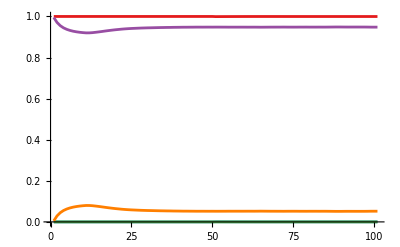

```mathematica
(*-----------------------------------*)
(*----------run the compiled code 'test' with the parameter fiel as input; put 'cout' output into cout-------*)
cout=Import["!./gdsimsapp<./Par"<>ToString[set]<>".csv","Table"];
(*---------------------------------------------------------------*)
(*----import the 'Totals..' output file with numbers of males in each genotype-------*)
totals=Drop[Import["./output_files/Totals"<>ToString[set]<>"run1.txt","Table"],2];
Dimensions[totals]
(*-----------------------------------------------------------------------*)

(*-------plot the output, both with arithmetic and log y-axis scale----------------------------------------*)
colours={Red,Blue,Green,Orange,Purple,Cyan};
(*ListLinePlot[Table[totals[[All,{1,i}]],{i,2,7,1}],PlotRange->All,PlotStyle->colours,PlotLegends->{"Mww","Mwd","Mdd","Mwr","Mrr","Mdr"}]
ListLogPlot[Table[totals[[All,{1,i}]],{i,2,7,1}],PlotRange->All,PlotStyle->colours,Joined->True,PlotLegends->{"Mww","Mwd","Mdd","Mwr","Mrr","Mdr"}];*)
{ww,ddd,rr,AA,BB}=allelefreq[totals];
cc={RGBColor[Rational[76, 85], Rational[26, 255], Rational[28, 255]],RGBColor[Rational[11, 51], Rational[42, 85], Rational[184, 255]],RGBColor[Rational[77, 255], Rational[35, 51], Rational[74, 255]],RGBColor[Rational[152, 255], Rational[26, 85], Rational[163, 255]],RGBColor[1, Rational[127, 255], 0],Black};
ListLinePlot[{ww,ddd,rr,AA,BB},PlotStyle->cc]
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
Last[totals]
```

{500,0,3,134,0,0,10,0,1,24,0,0,0,0,0,1,0,0,1}

```mathematica
18^3+1
```

5833

```mathematica
inher=cout[[2;;5833]];
Dimensions[inher]
```

{5832,4}

```mathematica
inher[[1;;18]]
```

{{0,0,0,1},{0,0,1,0},{0,0,2,0},{0,0,3,0},{0,0,4,0},{0,0,5,0},{0,0,6,0},{0,0,7,0},{0,0,8,0},{0,0,9,0},{0,0,10,0},{0,0,11,0},{0,0,12,0},{0,0,13,0},{0,0,14,0},{0,0,15,0},{0,0,16,0},{0,0,17,0}}

```mathematica
totals[[1;;3]]
```

{{Total,males,of,each,genotype},{Day,WWAA,WDAA,DDAA,WRAA,RRAA,DRAA,WWAB,WDAB,DDAB,WRAB,RRAB,DRAB,WWBB,WDBB,DDBB,WRBB,RRBB,DRBB},{0,50000,0,0,0,0,0,500,0,0,0,0,0,0,0,0,0,0,0}}

{5,2191}

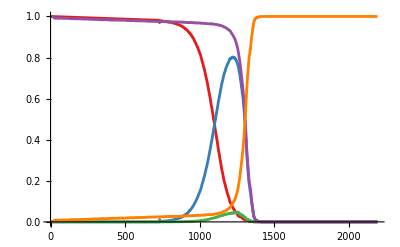

```mathematica
{ww,ddd,rr,AA,BB}=allelefreq[totals];
cc={RGBColor[Rational[76, 85], Rational[26, 255], Rational[28, 255]],RGBColor[Rational[11, 51], Rational[42, 85], Rational[184, 255]],RGBColor[Rational[77, 255], Rational[35, 51], Rational[74, 255]],RGBColor[Rational[152, 255], Rational[26, 85], Rational[163, 255]],RGBColor[1, Rational[127, 255], 0],Black};
ListLinePlot[{ww,ddd,rr,AA,BB},PlotStyle->cc]
```